```mathematica
Import["testdata.txt"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
test = Import["testdata.txt", "Table"]
```

{{0,0},{1,7507},{2,7356},{3,7580},{4,7285},{5,7481},{6,7489},{7,7613},{8,7473},{9,7528},{10,7565},{11,7478},{12,7455},{13,7563},{14,7624},{15,7639},{16,7530},{17,7680},{18,7546},{19,7526},{20,7925},{21,7799},32724,{32746,0},{32747,0},{32748,0},{32749,0},{32750,0},{32751,0},{32752,0},{32753,0},{32754,0},{32755,0},{32756,0},{32757,0},{32758,0},{32759,0},{32760,0},{32761,0},{32762,0},{32763,0},{32764,0},{32765,0},{32766,0},{32767,0}}
 |  |  |  |

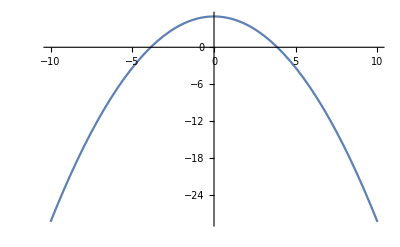

```mathematica
test = {{{{0,0},{1,7507},{2,7356},{3,7580},{4,7285},{5,7481},{6,7489},{7,7613},{8,7473},{9,7528},{10,7565},{11,7478},{12,7455},{13,7563},{14,7624},{15,7639},32736,{32752,0},{32753,0},{32754,0},{32755,0},{32756,0},{32757,0},{32758,0},{32759,0},{32760,0},{32761,0},{32762,0},{32763,0},{32764,0},{32765,0},{32766,0},{32767,0}}}, {{{, , , , }}}}
```

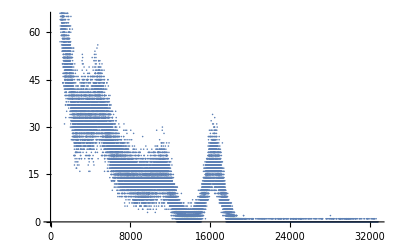

```mathematica
ListPlot[test]
```

```mathematica
Fit[test, {1, x, x^2, x^3, x^4, x^5, x^6, x^7}, x]
```

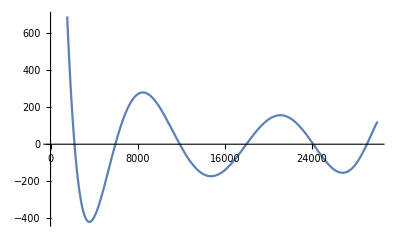

```mathematica
Plot[4529.02342777736-3.9400829009671683 x+0.0011497224838316782 x^2-1.5670961163703394*^-7 x^3+1.1285675069802256*^-11 x^4-4.42458825922669*^-16 x^5+8.923388393045036*^-21 x^6-7.245506608893939*^-26 x^7, {x, 0, 30000}]
```

```mathematica
test2 = Import["test2.txt", "Table"]
```

{{0,0},{1,18109},{2,18104},{3,18318},{4,18172},{5,18492},{6,18688},{7,18821},{8,18590},{9,19036},{10,19062},{11,19079},{12,19307},{13,19255},{14,19420},{15,19438},{16,19589},{17,19795},{18,20029},{19,19919},{20,20069},32726,{32747,0},{32748,0},{32749,0},{32750,0},{32751,0},{32752,0},{32753,0},{32754,0},{32755,0},{32756,0},{32757,0},{32758,0},{32759,0},{32760,0},{32761,0},{32762,0},{32763,0},{32764,0},{32765,0},{32766,0},{32767,0}}
 |  |  |  |

```mathematica
ListPlot[test2]
```

-Graphics-

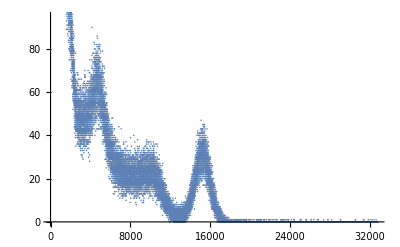

```mathematica
ListPlot[test]
```

```mathematica
test3 = Import["Na22.txt", "Table"]
```

{{0,0},{1,1578},{2,1520},{3,1541},{4,1576},{5,1675},{6,1704},{7,1787},{8,1747},{9,1750},{10,1813},{11,1816},{12,1806},{13,1847},{14,1834},{15,1858},{16,1954},{17,1978},{18,1955},{19,1879},{20,2091},{21,2106},32724,{32746,4},{32747,3},{32748,3},{32749,4},{32750,2},{32751,2},{32752,1},{32753,0},{32754,2},{32755,2},{32756,1},{32757,3},{32758,2},{32759,1},{32760,8},{32761,3},{32762,3},{32763,7},{32764,1},{32765,3},{32766,5},{32767,1}}
 |  |  |  |

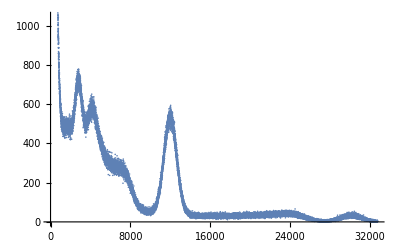

```mathematica
ListPlot[test3]
```